# Tuning the QFT computations

We check that the QFT computations give us the right computations. We perform the QFT computations and the exact computations and compare. 

The input of the QFT computations is a lattice Λ, an interaction tensor V, and an external magnetic field h. These inputs encode the Hamiltonian of the system

H = -(2 Σ_(v∈Λ) h(v)· S(v) +Σ_(v,w ∈Λ)S(v)·V(v, w)·S(w)) 

In particular,  we have

S(v) = (S_+(v), S_-(v), S_z(v)) with S_±(v) = S_x(v) ± i S_y(v)

and 

V(v,w) = (V_(i,j)(v,w))_(i, j = +, -, z)

We compare with the Hamiltonian for the XXX spin-1/2 chain. We take the lattice

Λ = {1, 2, …, λ}
H =- Σ_(k=1, ..., λ)2 h(k)· S(k) -J Σ_(k=1, ..., λ-1)S(k)·S(k+1) 

The corresponding interaction tensor in this case is 

V(k, k±1) = (0 | J/4 | 0
J/4 | 0 | 0
0 | 0 | J/2) and V(k, j) = 0 for j≠k±1

The QFT computations give a series approximation of the Quantum statistics partition function and correlation functions

Z[β] = Tr[e^(-β H)]
⟨S(v)⟩ = Tr[S(v)e^(-β H)]

where β= 1/(k T).

## Example: L=2 XXZ line

## QFT computations

### Lattice

```mathematica
L=2;
Λ = Table[{i, 0, 0}, {i, 1, L}];
λ = Length[Λ];
ListPointPlot3D[Λ,PlotStyle->{Blue,PointSize[0.05]}, Axes-> False, PlotRange->Full]
```

-Graphics3D-

### External Magnetic Field

```mathematica
hm=0;
hp=0;
hz=0.01;
HbExp[β_]:={{Cosh[√(hm hp+hz^2) β]+(hz Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2)),(hm Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2))},{(hp Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2)),Cosh[√(hm hp+hz^2) β]-(hz Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2))}};
```

### Interaction Tensors

#### Constants

```mathematica
a=1;
b=1;
c=1;
LS = {{a, 0, 0}, {0, b, 0}, {0, 0, c}};
Ja=1;
Jb=1;
Jc=1;
Ds =1;
βscaling = 1;
```

#### Spin-Spin exchange Interaction

```mathematica
V[v1_,v2_, s1_, s2_]:=Module[{r, dx, dy, dz},
r = Norm[(v1-v2)];
If[r!=1,Return[0] ];
dx= Norm[(v1-v2)[[1]]];
If[dx==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Ja/4], If[s1==3&&s2==3, Return[Ja/2]]]];
dy= Norm[(v1-v2)[[2]]];
If[dy==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Jb/4], If[s1==3&&s2==3, Return[Jb/2]]]];
dz= Norm[(v1-v2)[[3]]];
If[dz==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Jc/4], If[s1==3&&s2==3, Return[Jc/2]]]];
Return[0];
]
```

```mathematica
Table[V[Λ[[1]], Λ[[2]],s1, s2], {s1, 1, 3}, {s2, 1, 3}]//MatrixForm
```

(0 | Ja/4 | 0
Ja/4 | 0 | 0
0 | 0 | Ja/2)

### Correlation Function: Sz

```mathematica
acc = 2;
vIndex= 1;
sIndex=3;(*3->Subscript[S, z] spin operator*)
t=0;(*One-point correlations are independent of time b/c traces of linear operators are invariant under cyclic permutation of operators.*)
Tmin=2;
Tmax = 10;
Tdelta=1;
```

```mathematica
ZT = Table[{T, Z[acc,βscaling/T]}, {T,Tmin , Tmax, Tdelta}];
```

```mathematica
OzTun = Table[OnePoint[acc,βscaling/T, vIndex, sIndex, t], {T, Tmin, Tmax, Tdelta}];
```

```mathematica
OzT= Table[{ZT[[k]][[1]],OzTun[[k]]/ZT[[k]][[2]]}, {k, 1, Length[ZT]}];
```

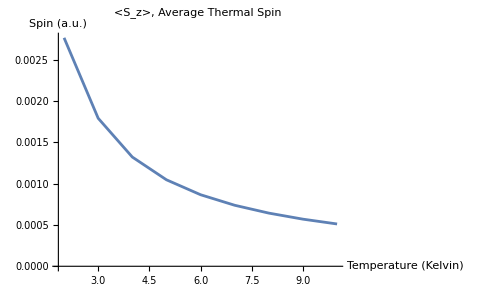

```mathematica
P1 =ListPlot[OzT, Joined->True, AxesLabel->{"Temperature (Kelvin)", "Spin (a.u.)"}, PlotLabel->"<S_z>, Average Thermal Spin"]
```

## Exact Computations

### Local Hamiltonians

```mathematica
h = (Ja/2)(KroneckerProduct[Sp, Sm] + KroneckerProduct[Sm, Sp]) + Ja (KroneckerProduct[Sz, Sz]);
Sz = {{1/2, 0}, {0 ,-1/2}};
```

### Hamiltonian

```mathematica
H =  -(Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h,IdentityMatrix[2^(λ-k-1)] ], {k, 1, λ-1}] + 2 Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], hz Sz, IdentityMatrix[2^(λ-k)]], {k, 1, λ}]);
```

```mathematica
MatrixForm[H]
```

(-0.02-Ja/4 | 0. | 0. | 0.
0. | 0.+Ja/4 | 0.-Ja/2 | 0.
0. | 0.-Ja/2 | 0.+Ja/4 | 0.
0. | 0. | 0. | 0.02-Ja/4)

### Expected Values

```mathematica
Zexact[β_]:= Tr[MatrixExp[  -β H]];
Sz1 =KroneckerProduct[Sz, IdentityMatrix[2]];
OzExactUn[β_] := Tr[Sz1.MatrixExp[- β H]];
```

### Plots

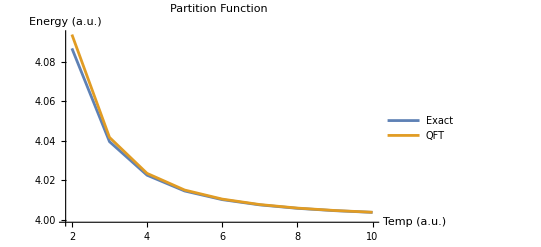

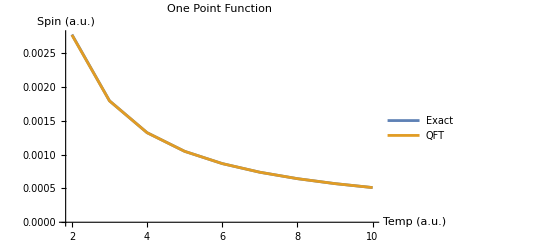

```mathematica
ZexactT = Table[{T, Zexact[βscaling/T]}, {T,Tmin , Tmax, Tdelta}];
OzExactUnT = Table[OzExactUn[βscaling/T], {T, Tmin, Tmax, Tdelta}];
OzExactT = Table[{ZexactT[[k]][[1]], OzExactUnT[[k]]/(ZexactT[[k]][[2]])}, {k, 1, Length[ZexactT]}];
ListPlot[{ZexactT, ZT}, PlotLegends->{"Exact", "QFT"}, Joined->True, PlotLabel->"Partition Function", AxesLabel->{"Temp (a.u.)", "Energy (a.u.)"}]
ListPlot[{OzExactT, OzT}, PlotLegends->{"Exact", "QFT"}, Joined->True, PlotLabel->"One Point Function", AxesLabel->{"Temp (a.u.)", "Spin (a.u.)"}]
```

## Example: L=3 XXZ line

## QFT computations

### Lattice

```mathematica
L=3;
Λ = Table[{i, 0, 0}, {i, 1, L}];
λ = Length[Λ];
ListPointPlot3D[Λ,PlotStyle->{Blue,PointSize[0.05]}, Axes-> False, PlotRange->Full]
```

-Graphics3D-

### External Magnetic Field

```mathematica
hm=0;
hp=0;
hz=0.01;
HbExp[β_]:={{Cosh[√(hm hp+hz^2) β]+(hz Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2)),(hm Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2))},{(hp Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2)),Cosh[√(hm hp+hz^2) β]-(hz Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2))}};
```

### Interaction Tensors

#### Constants

```mathematica
a=1;
b=1;
c=1;
LS = {{a, 0, 0}, {0, b, 0}, {0, 0, c}};
Ja=1;
Jb=1;
Jc=1;
Ds =1;
βscaling = 1;
```

#### Spin-Spin exchange Interaction

```mathematica
V[v1_,v2_, s1_, s2_]:=Module[{r, dx, dy, dz},
r = Norm[(v1-v2)];
If[r!=1,Return[0] ];
dx= Norm[(v1-v2)[[1]]];
If[dx==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Ja/4], If[s1==3&&s2==3, Return[Ja/2]]]];
dy= Norm[(v1-v2)[[2]]];
If[dy==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Jb/4], If[s1==3&&s2==3, Return[Jb/2]]]];
dz= Norm[(v1-v2)[[3]]];
If[dz==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Jc/4], If[s1==3&&s2==3, Return[Jc/2]]]];
Return[0];
]
```

### Correlation Function: Sz

```mathematica
acc = 2;
vIndex= 1;
sIndex=3;(*3->Subscript[S, z] spin operator*)
t=0;(*One-point correlations are independent of time b/c traces of linear operators are invariant under cyclic permutation of operators.*)
Tmin=2;
Tmax = 10;
Tdelta=1;
```

```mathematica
ZT = Table[{T, Z[acc,βscaling/T]}, {T,Tmin , Tmax, Tdelta}];
```

```mathematica
OzTun = Table[OnePoint[acc,βscaling/T, vIndex, sIndex, t], {T, Tmin, Tmax, Tdelta}];
```

```mathematica
OzT= Table[{ZT[[k]][[1]],OzTun[[k]]/ZT[[k]][[2]]}, {k, 1, Length[ZT]}];
```

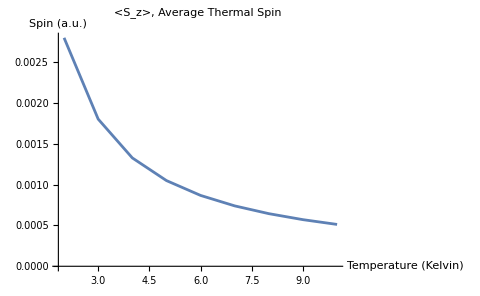

```mathematica
P1 =ListPlot[OzT, Joined->True, AxesLabel->{"Temperature (Kelvin)", "Spin (a.u.)"}, PlotLabel->"<S_z>, Average Thermal Spin"]
```

## Exact Computations

### Local Hamiltonians

```mathematica
h = (Ja/2)(KroneckerProduct[Sp, Sm] + KroneckerProduct[Sm, Sp]) + (KroneckerProduct[Sz, Sz]);
Sz = {{1/2, 0}, {0 ,-1/2}};
```

### Hamiltonian

```mathematica
H = -(Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h,IdentityMatrix[2^(λ-k-1)] ], {k, 1, λ-1}] + 2 Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], hz Sz, IdentityMatrix[2^(λ-k)]], {k, 1, λ}]);
```

### Expected Values

```mathematica
Zexact[β_]:= Tr[MatrixExp[ -β H]];
Sz1 =KroneckerProduct[Sz, IdentityMatrix[2^(λ-1)]];
OzExactUn[β_] := Tr[Sz1.MatrixExp[-β H]];
```

### Plots

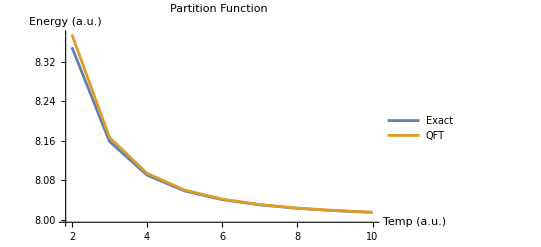

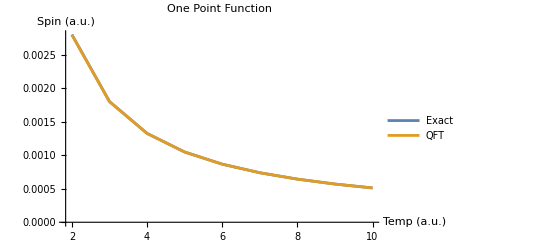

```mathematica
ZexactT = Table[{T, Zexact[βscaling/T]}, {T,Tmin , Tmax, Tdelta}];
OzExactUnT = Table[OzExactUn[βscaling/T], {T, Tmin, Tmax, Tdelta}];
OzExactT = Table[{ZexactT[[k]][[1]], OzExactUnT[[k]]/(ZexactT[[k]][[2]])}, {k, 1, Length[ZexactT]}];
ListPlot[{ZexactT, ZT}, PlotLegends->{"Exact", "QFT"}, Joined->True, PlotLabel->"Partition Function", AxesLabel->{"Temp (a.u.)", "Energy (a.u.)"}]
ListPlot[{OzExactT, OzT}, PlotLegends->{"Exact", "QFT"}, Joined->True, PlotLabel->"One Point Function", AxesLabel->{"Temp (a.u.)", "Spin (a.u.)"}]
```